## LOAD DATA

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["FlyGutData.csv"];

treatmenttmp=data⟦2;;-49,1⟧;
speciescollectiontmp=data⟦2;;-49,2;;6⟧;
absoluteabundancetmp=data⟦2;;-49,7;;11⟧;
```

Delete experiments with zero total abundance

```mathematica
speciescollection=Delete[speciescollectiontmp,Position[Total[#]&/@absoluteabundancetmp,0]];

absoluteabundance=Delete[absoluteabundancetmp,Position[Total[#]&/@absoluteabundancetmp,0]];

treatment=Delete[treatmenttmp,Position[Total[#]&/@absoluteabundancetmp,0]];
```

## ANALYSIS

Compute thresholds q for extinction, based on a ϵ constant.

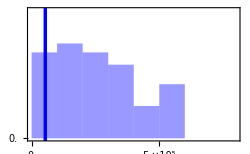

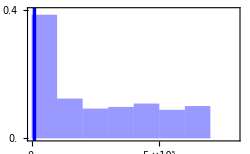

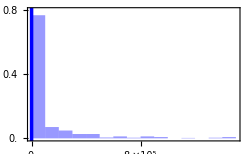

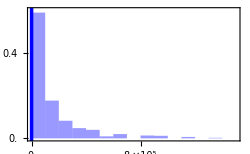

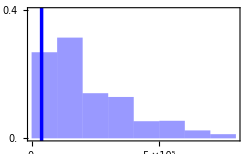

{53657.,11133.,0.,0.,39210.}

```mathematica
ϵ = 0.1;

x = Range[5];
q=Range[5];

Table[
indx = Flatten@Position[speciescollection⟦All,i⟧,_?(#==1&)];
x⟦i⟧ = absoluteabundance⟦indx,i ⟧;
q⟦i⟧=Quantile[x⟦i⟧,ϵ];
,{i,1,5}];

Histogram[{x⟦1⟧},{100000},"Probability",
Frame->True,
ChartStyle->Directive[Blue,Opacity[0.4],EdgeForm[None]],
GridLinesStyle->Directive[Blue,Thickness[0.01]],
GridLines->{{q⟦1⟧},None},
FrameTicksStyle->13,
ImageSize->250,
(*FrameTicks->{{Range[0,1,0.1],None},{Range[0,1000000,250000],None}},*)
FrameTicks->{{Range[0,1,0.1],None},{{#,ScientificForm@#}&/@Range[0.,10^6,250000.],None}},
PlotRange->{{0,800000},{0,0.3}}
]

Histogram[{x⟦2⟧},{100000},"Probability",
Frame->True,
ChartStyle->Directive[Blue,Opacity[0.4],EdgeForm[None]],
GridLinesStyle->Directive[Blue,Thickness[0.01]],
GridLines->{{q⟦2⟧},None},
FrameTicksStyle->13,
FrameTicksStyle->13,
ImageSize->250,
FrameTicks->{{Range[0,1,0.1],None},{{#,ScientificForm@#}&/@Range[0.,10^6,250000.],None}},
PlotRange->{{0,800000},{0,0.4}}
]

Histogram[{x⟦3⟧},{100000},"Probability",
Frame->True,
ChartStyle->Directive[Blue,Opacity[0.4],EdgeForm[None]],
GridLinesStyle->Directive[Blue,Thickness[0.01]],
GridLines->{{q⟦3⟧},None},
FrameTicksStyle->13,
FrameTicksStyle->13,
ImageSize->250,
FrameTicks->{{Range[0,1,0.2],None},{{#,ScientificForm@#}&/@Range[0.,2*10^6,400000.],None}},
PlotRange->{{0,1500000},{0,0.8}}
]

Histogram[{x⟦4⟧},{100000},"Probability",
Frame->True,
ChartStyle->Directive[Blue,Opacity[0.4],EdgeForm[None]],
GridLinesStyle->Directive[Blue,Thickness[0.01]],
GridLines->{{q⟦4⟧},None},
FrameTicksStyle->13,
FrameTicksStyle->13,
ImageSize->250,
FrameTicks->{{Range[0,1,0.2],None},{{#,ScientificForm@#}&/@Range[0.,2*10^6,400000.],None}},
PlotRange->{{0,1500000},{0,0.6}}
]

Histogram[{x⟦5⟧},{100000},"Probability",
Frame->True,
ChartStyle->Directive[Blue,Opacity[0.4],EdgeForm[None]],
GridLinesStyle->Directive[Blue,Thickness[0.01]],
GridLines->{{q⟦5⟧},None},
FrameTicksStyle->13,
FrameTicksStyle->13,
ImageSize->250,
FrameTicks->{{Range[0,1,0.1],None},{{#,ScientificForm@#}&/@Range[0.,10^6,250000.],None}},
PlotRange->{{0,800000},{0,0.4}}
]

q
```

Threshold abundances

```mathematica
extinctedabundances=Table[
temp=If[absoluteabundance⟦i,j⟧<=q⟦j⟧,0,absoluteabundance⟦i,j⟧]
,{i,1,Length@absoluteabundance},{j,1,5}];

extinctedabundances
```

{{313000.,0,0,0,0},{268000.,0,0,0,0},{224000.,0,0,0,0},{358000.,0,0,0,0},{268000.,0,0,0,0},{268000.,0,0,0,0},{268000.,0,0,0,0},{152000.,0,0,0,0},{179000.,0,0,0,0},{179000.,0,0,0,0},{179000.,0,0,0,0},1428,{358000.,89061,0,164000.,471000.},{0,256000.,0,245000.,353000.},{537000.,55663,49063,327000.,235000.},{0,0,32708,32708,141000.},{71543,334000.,164000.,409000.,549000.},{447000.,0,131000.,164000.,235000.},{161000.,0,0,81771,196000.},{447000.,33398,98125,229000.,549000.},{268000.,66796,32708,32708,267000.},{98371,0,49063,49063,180000.}}
 |  |  |  |

Calculate coexistance based on a threshold r. 
Namely, the species collection S coexist if the original and thresholded abundances have the same zero pattern for at least r% of the experiments.

```mathematica
r = 0.7;

localcommunities=DeleteDuplicates@speciescollection;

coexistence=Table[
indx = Flatten@Position[speciescollection, S];

temp=(Boole@SameQ[#,S]) &/@Abs@Sign@extinctedabundances⟦indx⟧;
If[Mean[temp]>r,1,0]
,{S,localcommunities}];

Thread[localcommunities-> coexistence]
```

{{1,0,0,0,0}→1,{0,1,0,0,0}→1,{0,0,1,0,0}→1,{0,0,0,1,0}→1,{0,0,0,0,1}→1,{1,1,0,0,0}→0,{1,0,1,0,0}→1,{1,0,0,1,0}→1,{1,0,0,0,1}→1,{0,1,1,0,0}→1,{0,1,0,1,0}→1,{0,1,0,0,1}→1,{0,0,1,1,0}→0,{0,0,1,0,1}→0,{0,0,0,1,1}→0,{1,1,1,0,0}→0,{1,1,0,1,0}→0,{1,1,0,0,1}→0,{1,0,1,1,0}→0,{1,0,1,0,1}→0,{1,0,0,1,1}→1,{0,1,1,1,0}→0,{0,1,1,0,1}→0,{0,1,0,1,1}→1,{0,0,1,1,1}→0,{1,1,1,1,0}→0,{1,1,1,0,1}→0,{1,1,0,1,1}→0,{1,0,1,1,1}→0,{0,1,1,1,1}→0,{1,1,1,1,1}→0}

Build hypergraph with the species collection that coexist.

```mathematica
indx =Flatten@Position[coexistence, 1];
hypergraph=Flatten@Position[#,1]&/@localcommunities⟦indx⟧
```

{{1},{2},{3},{4},{5},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{1,4,5},{2,4,5}}

## HYPERGRAPH VISUALIZATION

```mathematica
n = Max@Flatten[hypergraph]
edges = Flatten[{#⟦1⟧<->#⟦2⟧}&/@Cases[hypergraph,_?(Length[#]==2&)]]

hyperedges = Cases[hypergraph,_?(Length[#]==3&)]

g3d=Graph3D[Range[1,n],edges,
VertexLabels->"Name",
VertexLabelStyle->14,
BaseStyle->Blue,
EdgeStyle->Blue,
EdgeShapeFunction->({Blue,Tube[#1]}&),
VertexSize->0.07,
(*GraphLayout-> "HighDimensionalEmbedding"*)
GraphLayout->"SpringElectricalEmbedding"
];

coordinates=GraphEmbedding@g3d;
hyperedgecoordinates = coordinates⟦#⟧&/@hyperedges;

Show[
Table[
Graphics3D[{Blue,Opacity[0.5],Simplex[coords]}]
,{coords,hyperedgecoordinates}],
g3d,
Boxed->False,
ImageSize->400
]
```

5

{1<->3,1<->4,1<->5,2<->3,2<->4,2<->5}

{{1,4,5},{2,4,5}}

-Graphics3D-